```mathematica
PRÁCTICA  2
```

AUTOR : ÁNGEL IGUALADA MORAGA

# SESIÓN 1

## Ejercicio 1

```mathematica
AC[Inicial_List,Regla_Integer,t_Integer]:=Module[{listaDeListas,l,res,listaRes,cont,ant,pos,act,nuevoEstado,aux},
listaDeListas = MapThread[Append,{Tuples[{0,1},3],Reverse[IntegerDigits[Regla,2,8]]}];
res=Inicial;
listaRes={{Inicial}};
For[x=1,x≤t,x++,
l=Join[{Last[res]},res,{First[res]}];
nuevoEstado={};
For[i=1,i<=Length[Inicial],i++,
ant =l[[i]];
act= l[[i+1]];
pos =l[[i+2]];
AppendTo[nuevoEstado,FirstCase[listaDeListas,{ant,act,pos,estado_}->estado]];
];
res=nuevoEstado;
aux = Last[listaRes];
AppendTo[listaRes,Join[{res},aux]];
];
listaRes
]
```

### Comprobaciones

```mathematica
l=AC[{0,1,1,1,1,0,1},54,5];
lista1 =ListAnimate[Map[ArrayPlot,l]];
lista2 ={};
lista3={};
For[i=1,i≤Length[l],i++,
AppendTo[lista2,ArrayPlot[l[[i]],ColorRules->{0-> Red,1-> Black},PlotLegends->Placed[Automatic,Below],ImageSize->300]];
AppendTo[lista3,ArrayPlot[l[[i]],ColorFunction->"TemperatureMap",PlotLegends->Placed[Automatic,Below],ImageSize->300]];
];
{lista1 , ListAnimate[lista2],ListAnimate[lista3]}
```

{,,}

```mathematica
l=AC[{0,1,1,1,1,0,1,0,0,0,1,1,0,0,1},100,18];
lista1 =ListAnimate[Map[ArrayPlot,l]];
lista2 ={};
lista3={};
For[i=1,i≤Length[l],i++,
AppendTo[lista2,ArrayPlot[l[[i]],ColorRules->{0-> Yellow,1-> Black},ImageSize->300,PlotLegends->Placed[Automatic,Below]]];
AppendTo[lista3,ArrayPlot[l[[i]],ColorFunction->"Rainbow",PlotLegends->Placed[Automatic,Below],ImageSize->300]];
];
{lista1 , ListAnimate[lista2],ListAnimate[lista3]}
```

{,,}

```mathematica
l=AC[{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0},150,25];
lista1 =ListAnimate[Map[ArrayPlot,l]];
lista2 ={};
lista3={};
For[i=1,i≤Length[l],i++,
AppendTo[lista2,ArrayPlot[l[[i]],ColorRules->{0->Blue,1-> Black},ImageSize->300,PlotLegends->Placed[Automatic,Below]]];
AppendTo[lista3,ArrayPlot[l[[i]],ColorFunction->"Rainbow",PlotLegends->Placed[Automatic,Below],ImageSize->300]];
];
{lista1 , ListAnimate[lista2],ListAnimate[lista3]}
```

{,,}

### Comparaciones con RulePlot[CellularAutomaton] (definido en Mathematica)

```mathematica
mathematica1 = RulePlot[CellularAutomaton[150],{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0},25,ImageSize->300,FrameTicks->Automatic];
l=AC[{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0},150,25];
propio1 ={};
For[i=1,i≤Length[l],i++,
AppendTo[propio1,First[l[[i]]]];
]
{mathematica1,ArrayPlot[propio1,ImageSize->300,FrameTicks->Automatic]}
```

{-Graphics-,-Graphics-}

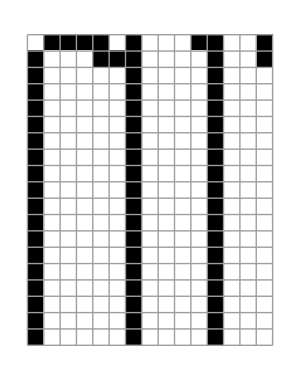
{-Graphics-,-Graphics-}

```mathematica
mathematica1 = RulePlot[CellularAutomaton[100],{0,1,1,1,1,0,1,0,0,0,1,1,0,0,1},18,ImageSize->300,FrameTicks->Automatic,Mesh->All];
l=AC[{0,1,1,1,1,0,1,0,0,0,1,1,0,0,1},100,18];
propio1 ={};
For[i=1,i≤Length[l],i++,
AppendTo[propio1,First[l[[i]]]];
]
{mathematica1,ArrayPlot[propio1,ImageSize->300,FrameTicks->Automatic,Mesh->All]}
```

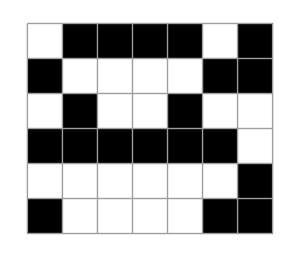
{-Graphics-,-Graphics-}

```mathematica
mathematica1 = RulePlot[CellularAutomaton[54],{0,1,1,1,1,0,1},5,ImageSize->300,FrameTicks->Automatic,Mesh->All];
l=AC[{0,1,1,1,1,0,1},54,5];
propio1 ={};
For[i=1,i≤Length[l],i++,
AppendTo[propio1,First[l[[i]]]];
]
{mathematica1,ArrayPlot[propio1,ImageSize->300,FrameTicks->Automatic,Mesh->All]}
```